## CellsOnBoundary-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Fri 9 Nov 2012 04:03:33
using xCellerator 0.90 and XSSA 1204002

Generate a random template constrained to  circle of radius 100 with at least 50 cells.  The actual number of cells will be the smallest integer square larger than 50.

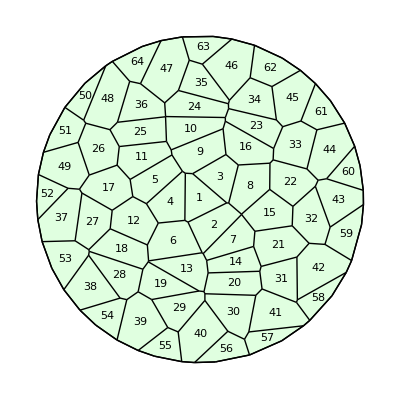

```mathematica
w=TemplateRandomCircularGrid[50,100];
ShowTissue[w, "CellNumbers"-> True]
```

```mathematica
n=NTissueCells[w]
```

64

Determine the cells that are on the "edge" of the tissue

```mathematica
cbw=CellsOnBoundary[w]
```

{37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

Color the "boundary" cells a different color.

```mathematica
n=NTissueCells[w];
colors=If[MemberQ[cbw,#], Pink, LightOrange]&/@Range[n];
```

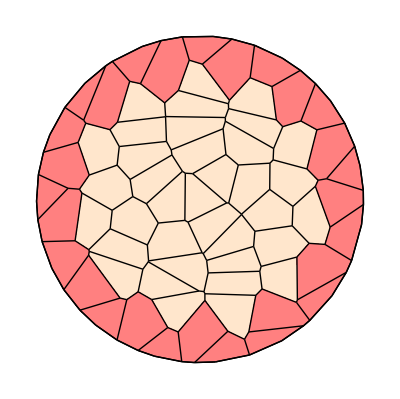

```mathematica
ShowTissue[w, "CellStyles"-> colors]
```

It will also identify interior boundary cells, such as those around an ablated center:

```mathematica
u=RemoveCell[w, {1,2,3}];
nu=NTissueCells[u];
cbu=CellsOnBoundary[u]; 
colors=If[MemberQ[cbu,#], Green, Purple]&/@Range[nu];
```

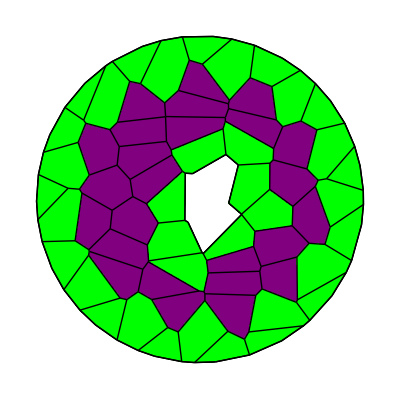

```mathematica
ShowTissue[u, "CellStyles"-> colors]
```